# Computational Chemistry

## Purpose

The purpose of this lesson is to...

provide an introduction to the common methods and basis sets in computational chemistry.

give an interpretation of the non-standardized and often nomenclature of computational chemistry.

introduce the pitfalls or advantages of each method and basis set.

provide examples of output from common computational chemistry packages.

## Learning Objectives

At the end of this lesson, I should be able to...

explain the construction of typical basis sets and how they account for the true shape of molecular orbitals through a linear combination of basis functions.

describe the advantages and disadvantages of different methods in computational chemistry.

interpret the output of electronic structure calculations.

## Overview of Approaches in Computational Chemistry

There are now many approaches in computational chemistry that may or may not be well-suited to the system you wish to investigate. This lesson won’t come close to covering all of these methods, but we’ll cover some of the most common techniques and the choices associated with each.

### Choose a Method

There are a multitude of approaches for calculating both static structures and properties and time-dependent dynamics of systems. A few of them are listed here:

Hartree-Fock calculations – we’ve already discussed the Hartree-Fock method several times in this course. Because this method only accounts for electron correlation relating to spin, it’s generally not very accurate and is not typically used in research anymore. However, as mentioned, the method forms the basis for other, more accurate approaches.

Møller–Plesset perturbation theory – these approaches involve perturbative corrections to the Hartree-Fock method,

( (Ĥ)^(0)+λ(Ĥ)^(1))ψ=E ψ

where (Ĥ)^(0)arises from a Fock operator, and (Ĥ)^(1)is known as the correlation potential. The most popular type of calculation is a second-order perturbation, known as MP2, but there are also higher-order perturbations (MP3, MP4, etc.).

Density Functional Theory – perhaps the most ubiquitous method in computational chemistry, this method is relatively cheap (meaning computationally quick) and accurate. There are numerous approximations within density functional theory, all of which use a slightly different combination of terms to estimate the electronic structure. Some of the most common approaches include B3LYP, PBE0, M06, and ωB97X.

Coupled cluster calculations – this approach also typically begins with the Hartree-Fock solutions and then takes a linear combination of the slater determinants of excited states. One approximation in particular, CCSD(T), is considered the gold standard for calculations on ground-state, closed-shell molecules. This approach is generally very expensive and can only be used for small molecules.

ab initio Molecular Dynamics (AIMD) – this approach involves a combination of traditional molecular dynamics, which don’t account for quantum mechanical effects, and electronic structure methods (MP2, DFT, etc.). It enables a more accurate, quantum-mechanical description of system dynamics, but it can’t account for nuclear quantum effects such as zero-point energy. There is a somewhat related method, ring polymer molecular dynamics (RPMD), that can account for nuclear quantum effects but is much more expensive.

These approaches are some of the most common employed for studying ground-state systems. To accurately predict electronic excited states, more advanced approaches are typically required.

### Choose a Basis Set

All of the methods listed above take a linear combination of atomic orbitals approach to solving for the molecular orbitals. The term “atomic orbitals” here does not represent the true atomic orbitals of an atom but rather an approximation formed by a basis set. The choice of basis set thus determines whether the full accuracy of the method can be achieved. If a basis set is too small, the results will be highly inaccurate because the molecular orbitals cannot be constructed. If it’s too large, the calculation will take too long to be practically useful.

## Some Common Basis Sets

### Slater-Type Orbitals (STOs)

Remember that we previously discussed the form of Slater-type orbitals,

ϕ_nlm^STO(r,θ,ϕ)=N_nl r^(n-1)Y_m^l(θ,ϕ)ⅇ^-ζr

where N_nl is a normalization constant, Y_m^l(θ,ϕ)is a spherical harmonic, and ζ represents a nuclear-charge-like parameter that controls the spatial extent of the orbital (how far from the nucleus the wavefunction extends). Typically, these are approximated in pseudo-Cartesian coordinates as

ϕ_abc^STO(x,y,z)=N x^a y^b z^c ⅇ^-ζr

In this format, the angular distribution (related to the angular momentum) is given by the constants a, b, and c. Note that these functions are not true spherical harmonics, and, as we discussed previously, the orbitals do not have nodes like true hydrogen-like atomic orbitals.

### Gaussian-Type Orbitals (GTOs)

Although older computational chemistry programs employed Slater-type orbitals, essentially all modern computational chemistry is performed with Gaussian-type orbitals (GTOs),

ϕ_abc^GTO(x,y,z)=N x^a y^b z^c ⅇ^(-ζr^2)

The reason for using Gaussian-type orbitals is something called the Gaussian product theorem, which, in short, states that the product of any two Gaussian functions centered on different atoms also yields a Gaussian function. This property greatly simplifies the calculation of integrals and speeds up computation.

We already discussed the difference in the radial dependence of Slater-type and Gaussian-type functions, as shown in Figure 12.1. The Gaussian-type orbital does not correctly match the behavior of a Slater-type orbital (which, remember, mimic the shape of a Hydrogen atomic orbitals). At long and short distance from the atomic nucleus, the Gaussian function fails to correctly predict the shape of the wavefunction.

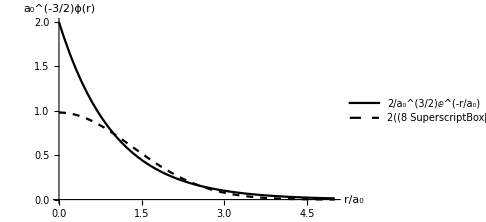

```mathematica
phi1s=(Integrate[Integrate[((1/(π*a^3))^(1/2)*ⅇ^(-r/a))^2 Sin[θ],{ϕ,0,2π}],{θ,0,π}])^(1/2);
phigauss=(Integrate[Integrate[(((2*(8/(9π*a^2)))/π)^(3/4)*ⅇ^(-(8/(9π*a^2))r^2))^2 Sin[θ],{ϕ,0,2π}],{θ,0,π}])^(1/2);

Plot[{phi1s/.a->1,phigauss/.a->1},{r,0,5},BaseStyle->{FontFamily->"Arial",FontSize->14},PlotStyle->{Directive[Black,PointSize[Large]],Directive[Black,Dashed,PointSize[Large]]},AxesStyle->Directive[Thick,Black],TicksStyle->Directive[Black, Thick],Ticks->Automatic,ImageSize->Medium, Exclusions->None,AxesOrigin->{0,0},AxesLabel->{"r/a_0","a_0^(-3/2)ϕ(r)"},PlotLegends->{"2/a_0^(3/2)ⅇ^(-r/a_0)","2((8 SuperscriptBox[α, 3])/π)^(1/4)ⅇ^(-αr^2)"}]
```

Figure 12.1. Plot of the radial component of the hydrogen 1s wavefunction (solid line) vs the Gaussian trial function optimized to yield the lowest energy (dashed line). The parameter α is given by α=8/(9π a_0^2).

To account for this difference, the Slater-type functions are typically replaced by a linear combination of Gaussian functions,

ϕ_abc^GTO(x,y,z)=N x^a y^b z^c(ⅇ^(-ζ_1 r^2)+ⅇ^(-ζ_2 r^2)+ⅇ^(-ζ_3 r^2))

An example of a three-term fitting to the radial component of a hydrogen 1s orbital is shown in Figure 12.2. Each Gaussian term in the sum is known as a primitive. The combination functions are typically labeled with the form STO–xG, where x gives the number of Gaussian terms. For example STO-3G would mean the Slater-type orbital is represented by a linear combination of three Gaussian functions, as in Figure 12.2.

2 √(ⅇ^(-(2 r)/a)/a^3)

FittedModel[0.594159 (ⅇ^(-5.00381 r^2)+ⅇ^(-0.897072 r^2)+ⅇ^(-0.20337 r^2))]

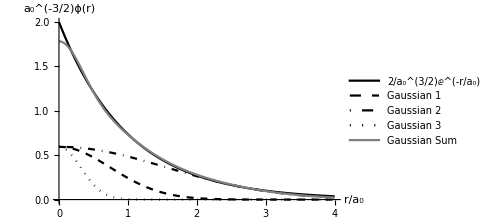

```mathematica
phi1s=(Integrate[Integrate[((1/(π*a^3))^(1/2)*ⅇ^(-r/a))^2 Sin[θ],{ϕ,0,2π}],{θ,0,π}])^(1/2)
phi1stable=Table[{r,phi1s/.a->1},{r,0.1,5,0.01}];
phigaussfit=NonlinearModelFit[phi1stable,n(ⅇ^(-l*r^2)+ⅇ^(-m*r^2)+ⅇ^(-k*r^2)),{l,k,m,n},r]
coeff=phigaussfit["ParameterTableEntries"][[All,1]];
Plot[{phi1s/.a->1,coeff[[4]]*ⅇ^(-coeff[[1]]*r^2),coeff[[4]]*ⅇ^(-coeff[[2]]*r^2),coeff[[4]]*ⅇ^(-coeff[[3]]*r^2),phigaussfit[r]},{r,0,4},PlotRange->Full,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotStyle->{Directive[Black,PointSize[Large]],Directive[Black,Dashed,PointSize[Large]],Directive[Black,DotDashed,PointSize[Large]],Directive[Black,Dotted,PointSize[Large]],Directive[Gray,PointSize[Large]]},AxesStyle->Directive[Thick,Black],TicksStyle->Directive[Black, Thick],Ticks->Automatic,ImageSize->Medium, Exclusions->None,AxesOrigin->{0,0},AxesLabel->{"r/a_0","a_0^(-3/2)ϕ(r)"},PlotLegends->{"2/a_0^(3/2)ⅇ^(-r/a_0)","Gaussian 1","Gaussian 2","Gaussian 3", "Gaussian Sum"}]
```

Figure 12.2. Fitting of a Slater-type function by a linear combination of Gaussian functions.

### Minimal Basis Sets

A minimal basis set includes only one basis function for each orbital in the Hartree-Fock (or similar) calculation. For 2^nd-row atoms, a minimal basis set also includes all of the p-type orbitals. For example, the minimal basis for a hydrogen atom would include only one 1s atomic orbital, whereas the minimal basis for a carbon atom would include the 1s, 2s, 2 p_x, 2 p_y, and 2 p_z orbitals. Basis sets such as STO–3G and STO–6G are minimal basis sets. These really aren’t used very often in modern computational chemistry.

### Double-Zeta, Triple-Zeta, and Split-Valence Basis Sets

Minimal basis sets struggle to accurately predict molecular structure and properties because they cannot sufficiently account for the full shape of the molecular orbitals. In particular, they inaccurately predict asymmetric bonding in polyatomic molecules, where the electron density of different bonds of an atomic center is asymmetric due to bonding with atoms of different electronegativity. This problem can be rectified by including multiple basis functions for each atomic orbital. For example, for a 2s atomic orbital, a double-zeta basis set would include the functions

ϕ_(2s)=a_1 ϕ_(2s)^GTO(ζ_1,r)+a_2 ϕ_(2s)^GTO(ζ_2,r)

where the weighting coefficients a_1 and a_2 would be optimized for a given molecular orbital. There are also triple-zeta basis sets and even quadruple-zeta or even higher basis sets.

To prevent double- or triple-zeta basis sets from becoming so large as to be computationally intractable, calculations are often performed with split-valence basis sets, in which the core electrons are represented by a minimal basis set, whereas the valence electrons are represented by a double- or triple-zeta basis set.

Note that when using these basis sets, the values of ζ_i are fixed for a given atom. In addition, the weighting factor a_1 is typically fixed (this may in fact comprise several weighting factors for different Gaussian components), and the factor a_2 is varied as part of the optimization.

### Pople Basis Sets

There are many forms of split-valence basis sets, but some of the historically most popular basis sets are those developed by John Pople and co-workers. The nomenclature for these basis sets is

n–mpG

where n specifies the number of Gaussians terms in the core basis functions (STO–nG), and m and p give the number of Gaussian primitives used to construct each double-zeta valence orbital. In other words, each valence atomic orbital is constructed of two basis functions, one with m primitive gaussian functions (typically optimized as a “contracted” orbital) and one with p primitive gaussian functions (optimized for an “extended” orbital).

One of the most popular Pople basis sets is 6-31G, which has a STO-6G representation for each core atomic orbital, and valence orbitals constructed from two basis functions (a double-zeta basis), one which is a linear combination of three Gaussian functions and one which is just a single Gaussian function. Another popular basis set is 6-311G, which is a bit newer and doesn’t quite follow the nomenclature above; the extra one represents an additional orbital component (triple-zeta basis) with just one Gaussian primitive.

### Polarization and Diffuse Functions

Although we have used double- and triple-zeta basis sets to address the issue of differences in electron density between different bonds (different atoms binding to a central carbon, for example), we haven’t yet addressed the polarization inherent in forming a molecular bond, which distorts the symmetric electron density around an atom. Take the example of a σ bond in H_2, where the electron density about each hydrogen is not spherically symmetric. To account for this asymmetry, we can include an additional 2p orbital, which can then be added to the previous basis of a 1s orbital to create a molecular orbital that is asymmetric with respect to hydrogen. Such additional atomic orbitals in a basis set are known as polarization functions.

The above example relates to polarization of s atomic orbitals by addition of p-type orbitals. Similarly, d-type orbitals can be added to p-type orbitals to generate polarized orbitals, as shown in Figure 12.3

```mathematica
Import["https://upload.wikimedia.org/wikipedia/commons/a/a7/D-polarization_function.png"]
```

-Graphics-

Figure 12.3. Linear combination of p and d orbitals to generate a polarized p orbital. Wikimedia, Rifleman82, CC BY-SA 3.0, https://commons.wikimedia.org/wiki/File:D-polarization_function.png

Different basis sets utilize different terminology to denote the addition of polarization functions. A useful table is provided at https://gaussian.com/basissets/. For the Pople basis sets, the polarization functions are noted with the terminology (d, p), where the d symbol denotes the addition of one set of 3d orbitals to the basis of second-row elements, and the p specifies the addition of one set of 2p orbitals to the hydrogen and/or helium atoms. Previously, an older nomenclature of ** was used (where the first star corresponds to d and the second star corresponds to p).

Recall that the Gaussian-type orbitals do not accurately depict the shape of the wavefunction at large distances from the nucleus (see, for example, Figure 12.1). To provide a more accurate depiction of the electron density at large distances from the nucleus, we can add additional diffuse functions to the basis set. These functions have a small value of the exponent ζ, meaning that the electron is likely to be found far from the nucleus. Such basis functions are especially important for calculating the structure of anions and molecules containing highly electronegative atoms such as fluorine. In the Pople basis sets, the addition of diffuse functions is indicated by a + sign or two + signs (e.g. 6-311+G(d,p)).

### Correlation-Consistent Basis Sets

Another widely utilized class of basis sets are the correlation-consistent basis sets developed by Thom Dunning and co-workers. Because the Pople basis sets were first optimized at the Hartree-Fock level of theory, there was concern that these basis sets might not be ideal for computations that account for electron correlation, such as MP2, CCSD(T), and DFT. The correlation-consistent (cc) basis sets were optimized using configuration interaction calculations that take into account electron correlation.

The Dunning correlation-consistent basis sets are split-valence basis sets that add additional basis functions in “shells” when increasing the number of basis functions. For example, for the 2^nd-row elements, the cc-pVDZ (correlation-consistent, polarized, valence double-zeta) basis set adds an extra set of s, p, and d orbitals to the minimal basis for a total of fourteen basis functions. The corresponding valence triple-zeta basis set, cc-pVTZ, adds a further set of s, p, d, and f orbitals to the double-zeta basis for a total of thirty basis functions.

Polarization functionality is already built into the basis sets by the addition of an extra set of orbitals in the basis set (for example, the extra d orbitals in the double-zeta basis set). Diffuse functions can also be added, which is typically specified by the addition of the prefix aug to the basis set name (e.g., aug-cc-pVTZ).

The correlation-consistent basis sets are also designed to converge smoothly, meaning the energies at each level of calculation can be fitted to extrapolate the energy in the complete-basis-set (CBS) limit. This concept is illustrated in Figure 12.4. By performing a fit of the energies calculated with different sizes of the basis sets, one can extrapolate the hypothetical energy with a basis set of infinite size, known as the complete-basis-set energy, or E_CBS.

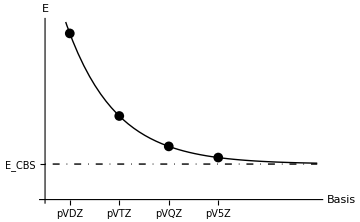

```mathematica
data=Table[{n,Exp[-n]+1},{n,1,4}];
Show[
Plot[{Exp[-x]+1,1}, {x,0.5,6},PlotRange->{{0.5,6},{0.9,1.4}},
BaseStyle->{FontFamily->"Arial",FontSize->16},PlotStyle->{Directive[Black,Thick],Directive[Black,Thick,DotDashed],Directive[Black,Dashed,Thin]},AxesStyle->Directive[Thick,Black],TicksStyle->Directive[Black, Thick],Ticks->{{{1,"pVDZ"},{2,"pVTZ"},{3,"pVQZ"},{4,"pV5Z"}},{{1,"E_CBS"}}},ImageSize->Medium, Exclusions->None,AxesOrigin->{0.5,0.9},AxesLabel->{"Basis","E"}]
,
ListPlot[data,BaseStyle->{FontFamily->"Arial",FontSize->16},PlotStyle->Directive[Black,Thick],PlotMarkers->{Automatic,Medium}]
]
```

Figure 12.4. Example of the extrapolation of the complete-basis-set energy (E_CBS) using the correlation-consistent basis sets.

### Additional Basis Sets

There are far too many basis sets to cover all of them here, but we will briefly introduce a few additional popular classes of basis sets.

The so-called Karlsruhe basis sets are likewise split-valence double- or triple-zeta basis sets, but they are optimized based on achieving the lowest possible energy (which, remember, in the variational method, is another way of saying the most accurate energy). They are given the prefix def2, for example def2-TZVP (def2 triple-zeta valence with polarization) or def2-QZVPPD (def2 quadruple-zeta valence with double polarization and diffuse functions).

There are also basis sets that have been optimized for DFT rather than post-Hartree-Fock (MP2, CCSD(T), etc.) methods. One popular class of these basis sets are the polarization-consistent (pc) basis sets developed by Jensen and co-workers. These are designed to enable a similar complete-basis-set extrapolation to that for the cc basis sets, in this case using DFT instead of a post-Hartree-Fock method.

Finally, a brief note about heavier atomic elements: when the atomic number is larger, as in many transition metals, relativistic effects become important in describing the behavior of the electrons, and these are not accounted for in typical computational chemistry approaches. Therefore, for larger atoms, an effective core potential (ECP) that empirically accounts for relativistic effects is typically incorporated into the basis set.

## Post Hartree-Fock Methods - Overview

We already discussed briefly in the introduction some of the so-called post Hartree-Fock methods such as MP2 and CCSD(T). Here we will give a little more information about the general approach taken by these methods.

### Failings of the Hartree-Fock Method

As we have already discussed, the Hartree-Fock method assumes that (excluding spin) the behavior of the electrons is not correlated, which allows us to write the wavefunction as an antisymmetrized product of the individual spin-orbital wavefunctions given by the Slater determinant.

ψ_Slater(1,2,...,N)=1/(√(N!))|χ_1(1) | χ_2(1) | ... | χ_N(1)
χ_1(2) | χ_2(2) | ... | χ_N(2)
... | ... | ... | ...
χ_1(N) | χ_2(N) | ... | χ_N(N)|

Remember that in this picture, each electron interacts only with the average charge distribution of all of the other electrons given by the effective potential. Thus, correlated interactions between electrons are not accounted for, leading to the so-called correlation energy error. Remember that dispersion interactions are the result of electron correlation, so clearly this error can be rather substantial and even lead to wholly incorrect predictions about the structure and behavior of molecules.

### Linear Combination of Slater Determinants

Although the single-Slater-determinant wavefunction is not exact, it is properly antisymmetrized. In principle, we can write the exact wavefunction as a linear combination of many different Slater-determinant wavefunctions

ψ_exact=∑_i ψ_Slater_i

But what would be the other Slater determinants besides the one from Hartree-Fock theory? Well, in short, they are excited-state functions, that is, wavefunctions in which one or more of the electrons are not in the ground-state molecular orbitals. The technique of configuration interaction (CI) involves taking all of the possible combinations of electron configurations for a given basis set, but it’s so computationally intensive as to be impractical for all but the smallest systems.

Typically, the types of excitations are grouped together based on the number of excited (i.e., non-ground-state) electrons,

|ψ⟩=c_0|ϕ_0⟩+∑c_i^a|ϕ_i^a⟩+∑c_ij^ab|ϕ_ij^ab⟩+∑c_ijk^abc|ϕ_ijk^abc⟩+...

where |ϕ_0⟩ is the reference ground-state Slater determinant from HF theory, and |ϕ_(ijk...)^(abc...)⟩ represents a Slater determinant where the orbitals i, j, k, ... have been replaced with the orbitals a, b, c, ... The second term in equation (10) represents single excitations, the third term represents double excitations, and so on.

The exact method to determine the coefficients and determinants in equation (10) becomes quite complicated. As mentioned, MP2 uses a variational treatment to determine the coefficients, and it turns out that the second-order correction to the energy depends only on the double excitation terms. Coupled-cluster calculations also involve a specific combination of excitations given by excitation operators.

## Density Functional Theory

We will now provide a brief overview of density functional theory (DFT). Because the fundamental assumptions of DFT are quite different from those of Hartree-Fock theory, we begin with an introduction to the underlying principles.

### Hohenberg-Kohn Theorems

The two theorems of Hohenberg and Kohn, formulated in the 1960s, represent the starting point for DFT. The basic idea is that the electronic wavefunction can be replaced by an electron density.

#### Theorem 1

For a system of electrons moving in an external potential v_ext(r), the potential is uniquely determined by the electron density ρ(r).

In more simple language, one might say that the ground-state properties of a system of electrons are given by the electron density function ρ(r).

#### Theorem 2

The energy of the system can be written as a functional of the density ρ(r). For an external potential v_ext(r), the exact ground-state energy E[ρ(r)] is given by the global minimum value of this functional.

A functional is just a function that depends on a function. This theorem indicates that if the energy is minimized by a variational method by modifying the density ρ(r), the lowest achievable energy will be the best approximation to the ground state of the system. If we find the true global minimum energy of the functional, this value will be the exact ground-state energy of the system.

Usually, the energy functional is written in the form

E[ρ(r)]=F[ρ(r)]+∫v_ext(r)ρ(r)ⅆr

where F[ρ(r)] is some unknown, universal functional of the electron density.

### Finding the Density Functional

We need some way to find the form of the density functional. Recall that the electronic Hamiltonian (neglecting internuclear repulsion) takes the form

(Ĥ)_e=(T̂)_e+(V̂)_eN+(V̂)_ee

If we now represent our energy as dependent on the electron density function ρ, we can then write

E[ρ]=T_e[ρ]+E_eN[ρ]+E_ee[ρ]

We know that the electron-nuclear interaction term should take the form

E_eN[ρ]=∑_A ∫(Z_A ρ(r))/(|r-R_A|)ⅆr

and we can write the form of the interaction of the electron density with itself, a sort of self-coulomb repulsion,

J[ρ]=1/2∫∫(ρ(r)ρ(r'))/(|r-r'|)ⅆrⅆr'

But so far, we don’t know the form of the density functional, and we don’t know the form of T_e[ρ]or the full form of V_ee[ρ].

### Kohn-Sham DFT

The Kohn-Sham approach to solving the problem of the electron density is to assume that the ground-state density of an interacting system can be represented by solving some equal non-interacting system where the electrons move in a single-particle potential. This approach is something like the Hartree approximation for a standard wavefunction; now the density can be written as a Slater determinant wavefunction,

ψ_KS=1/(√(N!))|χ_1(x_1)χ_2(x_2)... χ_N(x_N)|

and we can solve the problem by an approach analogous to the Hartree-Fock method!

In the Kohn-Sham approach, the energy is given by

E[ρ]=T_s[ρ]+E_eN[ρ]+J[ρ]+E_xc[ρ]

where T_s[ρ] is the Kohn-Sham kinetic energy, representing the kinetic energy of a non-interacting electron gas, and E_xc[ρ]is the exchange-correlation energy functional, which can be defined as

E_xc[ρ]=(T[ρ]-T_s[ρ])+(E_ee[ρ]-J[ρ])

In other words, E_xc[ρ]represents all of the energy contributions that are not accounted for when we switch from the interacting picture of Hohenberg-Kohn to the non-interacting picture of Kohn-Sham. The problem is, we don’t know the form of this functional, and we can only use approximate forms. The difference between all of the many DFT methods is the approximate form of the exchange-correlation functional that they use.

### Solving for the Kohn-Sham Orbitals

As mentioned, the Kohn-Sham DFT approach closely resembles the Hartree-Fock method. Instead of the Fock operator, we have the Kohn-Sham Hamiltonian,

(ĥ)_KS(r)ϕ_i(r)=ϵ_i ϕ_i(r)

Note that in this equation we’re only looking at spatial “orbitals”, but the equation for both spin and spatial components would be similar. The Kohn-Sham Hamiltonian is given by

(ĥ)_KS(r)=-1/2∇^2 +(V̂)_eN(r)+∫(ρ(r'))/(|r-r'|)ⅆr'+(V̂)_xc(r)

where the first term represents the kinetic energy operator of a non-interacting electron gas. Again, here, the form of (V̂)_xc(r)is unknown, so different DFT methods involve different approaches to approximate the form of this term.

Because DFT has a similar formulation to Hartree-Fock, it has a similar computational cost. However, because correlation is taken into account through the exchange-correlation term, the accuracy can be much higher than Hartree-Fock. Note that this accuracy depends strongly on the form of (V̂)_xc(r), and there is no systematic way to improve accuracy (unlike in post-Hartree-Fock methods).

### The Exchange-Correlation Potential

We now want to find some form of the exchange-correlation potential that we can use to compute the electronic structure and energy of molecules. Let us first examine the exchange-correlation energy, separating the energy into exchange and correlation terms,

E_xc[ρ]=(T[ρ]-T_s[ρ])+(E_ee[ρ]-J[ρ])
	    =E_c[ρ]+E_x[ρ]
	    =∫ρ(r)ϵ_c[ρ(r)]ⅆr+∫ρ(r)ϵ_x[ρ(r)]ⅆr

where ϵ_c and ϵ_x are the correlation and exchange energy per particle, respectively. Note that these are also functionals of the density.

The relationship between the exchange-correlation energy and the exchange-correlation potential is given by the equation

V_xc[ρ]=(∂E_xc[ρ])/(∂ρ)

Again, the goal of different DFT methods is to find the most accurate possible form of this exchange-correlation energy (and thus potential) that is computationally tractable.

### Classes of DFT Exchange-Correlation Functionals

#### Local Density Approximation (LDA) Functionals

One of the first exchange-correlation energy forms developed is known as the local density approximation (LDA). In the LDA, the exchange and correlation terms are based on a uniform gas model. Importantly, the exchange contribution depends only on the magnitude of the electron density at a given point in space. In equation form, this is sometimes represented as

E_x^LDA[ρ]=∫ρ(r)ϵ_x[ρ(r)]ⅆr

More exactly, the energy is given by the Dirac electron gas model as

E_x^LDA[ρ]=-c∫ρ^(4/3)(r)ⅆr

where c is a constant.

This approximation is not used very often in modern research because it gives inaccurate results for both the exchange and correlation components of the energy.

#### Generalized Gradient Approximation (GGA) Functionals

In reality, the electron density in molecules can change rapidly over a short distance, so the homogeneous electron gas model doesn’t work very well. To correct for this reality, the generalized gradient approximation assumes that the exchange contribution to the energy depends not only on the electron density at a given point in space but also on its gradient, or rate of change. In equation form, we can make this relationship more clear by writing

E_x^GGA[ρ]=∫ρ(r)ϵ_x[ρ(r),∇ρ]ⅆr

Sometimes, these functionals represent a mix of different components for the exchange terms (such as B88, also called B) and correlation terms (for example, LYP). BYLP would be an example of a full GGA functional. Other methods include PBE and PW91 (which also require some selection of the correlation functionals). Unfortunately, even with this improved approximation, these functionals still cannot produce a sufficiently accurate exchange contribution, so they are also not used so often.

There are also meta-GGA functionals, in which the exchange-correlation energy depends also on the Laplacian (second derivative) of the electron density. Examples of such functionals include TPSS and M06L.

#### Hybrid Methods

By far the most commonly utilized DFT methods utilize hybrid functionals. In short, these methods incorporate a portion of exchange from the Hartree-Fock method into the exchange-correlation energy obtained from an LDA or GGA functional. For example, the famous B3LYP exchange-correlation energy is given by

E_xc^B3LYP[ρ]=E_x^LDA+a_0(E_x^HF-E_x^LDA)+a_x(E_x^GGA-E_x^LDA)+E_c^LDA+a_c(E_c^GGA-E_c^LDA)

where a_0, a_x, and a_c are constants optimized empirically.

There are many other examples of hybrid functionals, for example PBE0, ωB97X, TPSSh, M06-2X, etc. Each have their own unique formulations for mixing the Hartree-Fock exchange with the GGA or LDA exchange and may also differ in the correlation potential. Again, there’s no hierarchy to which of these may be more or less accurate, and it may depend on the system being studied.

More recently, double-hybrid methods have been developed that also incorporate an MP2-like contribution to the correlation energy. These methods are typically more accurate, but they sacrifice the computational efficiency of DFT by requiring MP2 calculations.